# Soft AND

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

Payani (2020): “Differentiable Neural Logic Networks”

```mathematica
PayaniSoftAND[b_,w_]:=1-w (1-b)
```

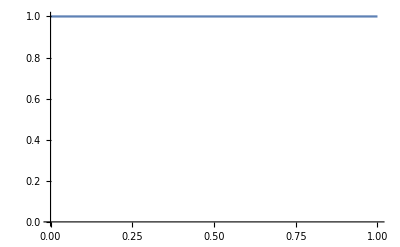

```mathematica
Plot[PayaniSoftAND[b,0],{b,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}}]
```

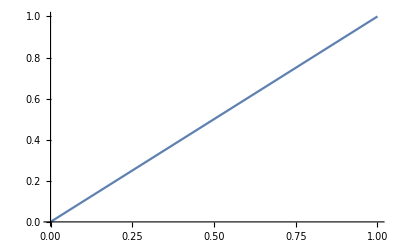

```mathematica
Plot[PayaniSoftAND[b,1],{b,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}}]
```

```mathematica
Manipulate[Plot[PayaniSoftAND[b,w],{b,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}}],{w,0,1}]
```

```mathematica
BooleanSoftAND[b_,w_]:=b||!w
```

```mathematica
Manipulate[
GraphicsRow[{
Plot[PayaniSoftAND[b,w],{b,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}},AxesLabel->Automatic],
DiscretePlot[Boole[BooleanSoftAND[Harden[b],Harden[w]]],{b,0,1},ExtentSize->Full,Filling->Axis,AxesLabel->Automatic]
}],
{w,0,1}
]
```

```mathematica
na=NeuralAND[2,4]
```

NetGraph[<>]

```mathematica
InitializeToConstant[na,0][{0.2,0.3}]
```

{1.,1.,1.,1.}

```mathematica
InitializeToConstant[na,1][{0.2,0.3}]
```

{0.0600001,0.0600001,0.0600001,0.0600001}

```mathematica
InitializeToConstant[na,1][{0.9,0.3}]
```

{0.27,0.27,0.27,0.27}

```mathematica
InitializeToConstant[na,1][{0.9,0.8}]
```

{0.72,0.72,0.72,0.72}

```mathematica
InitializeToConstant[na,1][{0.8,0.6}]
```

{0.48,0.48,0.48,0.48}